# MGDrivE: Yorkeys Knob Analysis

## 0) Functions

```mathematica
<<colorBlender`
rgbColors={
ColorData[{"LakeColors",{1,0}}][1],
ColorData[{"LakeColors",{1,0}}][0]
};
GenerateBlendSetting[color_]:=Module[{levels},
levels=Level[color,1];
{
RGBColor[levels[[1]],levels[[2]],levels[[3]],0],
RGBColor[levels[[1]],levels[[2]],levels[[3]],1]
}
]
GenerateBlendSettingCMYK[color_]:=Module[{levels},
levels=Level[color,1];
{
RGBColor[levels[[1]],levels[[2]],levels[[3]],0],
RGBColor[levels[[1]],levels[[2]],levels[[3]],1]
}
]
hexifyColor[color_RGBColor]:=StringJoin["#",IntegerString[Round[Level[color,1]*255],16,2]]
hexToRGB=RGBColor@@(IntegerDigits[ToExpression@StringReplace[#,"#"->"16^^"],256,3]/255.)&;
FixDataEntry[dataFileContent_]:=Append[#,#//Total]&/@(dataFileContent[[2;;All,2;;All]][[All,1;;(Length[dataFileContent[[1]]]-1)]])
PlotDynamics[data_,ranges_,colorPalette_,plotLabels_]:=Module[{plotRight,plotLeft},
(**)
plotLeft=ListLinePlot[
data//Transpose,
AspectRatio->1,
PlotTheme->"MGDrivE_PopDyn",
PlotStyle->colorPalette,
ImageSize->Large,
PlotRange->{{0,ranges[[1]]},{0,ranges[[2]]}},
FrameStyle->{
{Thick,Thick},
{Thick,Thick}
},
FrameTicks->Automatic,
FrameLabel->(Style[#,30]&/@plotLabels)
]
]
Themes`AddThemeRules["MGDrivE_PopDyn",
DefaultPlotStyle->Thread@Directive[colorPalette,Thickness[.01]],
LabelStyle->15,
Frame->True,
FrameStyle->Directive[Thick,Gray],
FrameTicksStyle->Gray,
GridLines->Automatic,
PlotRange->{0,All},
ImageSize->Large,
FrameLabel->(Style[#,30]&/@{"Time","Population"})
];
Options[SplitPlotDynamics]={AspectRatios->{.75,.45},ImageSize->500};
SplitPlotDynamics[data_,ranges_,colorPalette_,OptionsPattern[]]:=Module[{plotRight,plotLeft,rangeA=ranges[[1]],rangeB=ranges[[2]]},
(**)
plotLeft=ListLinePlot[
data//Transpose,
AspectRatio->1/OptionValue[AspectRatios][[1]],
PlotTheme->"MGDrivE_PopDyn",
PlotStyle->colorPalette,
ImageSize->{Automatic,OptionValue[ImageSize]},
PlotRange->{rangeA,{0,Round[(Flatten[data]//Max)*.1]+(Flatten[data]//Max)}},
FrameStyle->{
{Thick,Dashed},
{Thick,Thick}
},
FrameTicks->{{Automatic,None},{Range[0,rangeA[[2]]-1,100],None}},
FrameLabel->(Style[#,30]&/@{"Time","Population"})
];
plotRight=ListLinePlot[
data//Transpose,
AspectRatio->1/OptionValue[AspectRatios][[2]],
PlotTheme->"MGDrivE_PopDyn",
PlotStyle->colorPalette,
ImageSize->{Automatic,OptionValue[ImageSize]},
PlotRange->{rangeB,{0,Round[(Flatten[data]//Max)*.1]+(Flatten[data]//Max)}},
FrameStyle->{
{Dashed,Thick},
{Thick,Thick}
},
FrameTicks->{{None,All},{Range[0,rangeB[[2]]-1,500],None}},
FrameLabel->(Style[#,30,White]&/@{"Time","Population"})
];
Grid[{{plotLeft,plotRight}},Spacings->{0,0}]
]

ImportAndReshapeData[folderName_]:=Module[{fileNames,raw,data,dataTotal,maleFileNames,femaleFileNames,rawMale,rawFemale,dataMale,dataFemale,dataTotalMale,dataTotalFemale,genotypes},
fileNames={maleFileNames,femaleFileNames}=FileNames[folderName<>"/"<>#]&/@{"ADM*.csv","AF1_Aggregate*.csv"};
raw={rawMale,rawFemale}=Table[ParallelMap[Import[#]&,i],{i,fileNames}];
data={dataMale,dataFemale}=Table[#[[2;;All,3;;All]]&/@i,{i,raw}];
dataTotal={dataTotalMale,dataTotalFemale}=Table[Flatten/@Transpose[{Total/@#,#}]&/@i,{i,data}];
genotypes=Prepend[rawMale[[1,1,3;;All]],"Total"];
{genotypes,dataTotal}
]
CalculateQuartiles[genotypes_,data_]:=Module[{sexes,quartilesData,lowQuartile,medianQuartile,topQuartile},
sexes=2;
Table[
quartilesData=Table[Transpose[Quartiles/@Transpose[data[[j]][[All,All,i]]]],{i,1,genotypes//Length}];
{lowQuartile,medianQuartile,topQuartile}={quartilesData[[All,1]]//Transpose,quartilesData[[All,2]]//Transpose,quartilesData[[All,3]]//Transpose}
,{j,1,sexes}]
]
CreateColorSwatch[genotypes_,colorSchemeNumber_,{markerSize_,labelStyle_}]:=Module[{colorPalette,colorPairs,colorSwatch},
colorPalette=Prepend[ColorData[colorSchemeNumber,"ColorList"][[1;;(Length[genotypes]-1)]],Lighter[Black,.75]];
colorPairs=Transpose[{genotypes,colorPalette}];
colorSwatch=SwatchLegend[colorPairs[[All,2]],colorPairs[[All,1]],LegendMarkerSize->markerSize,LabelStyle->labelStyle,LegendLayout->{"Column",1}];
{colorPalette,colorSwatch}
]
ReshapeSexData[sexData_,quantile_]:=Module[{nodeDataAtTime,reshapedData},
reshapedData=Table[
Table[
nodeDataAtTime=Transpose[sexData][[node,All,time]];
Quantile[#,quantile]&/@Transpose[nodeDataAtTime]
,{time,1,sexData[[1,1]]//Length}]
,{node,1,sexData[[1]]//Length}];
reshapedData
]
ReshapeStochasticMultiNode[dataTotal_,quantile_]:=ParallelTable[ReshapeSexData[dataTotal[[All,i]],quantile],{i,1,2}]
AddLabelsToReshapedDataNode[reshapedDataNode_,genotypes_,patchNumber_]:=Module[{breakdownWithPop,breakdownWithTime,labels},
breakdownWithPop=Prepend[#,patchNumber]&/@reshapedDataNode[[All,2;;All]];
breakdownWithTime=Prepend[#[[2]],#[[1]]]&/@Transpose[{Range[breakdownWithPop//Length],breakdownWithPop}];
labels=Prepend[ReplacePart[genotypes,1->"Patch"],"Time"];
Prepend[breakdownWithTime,labels]
]
```

```mathematica
SmoothHistogramPlot[sampledCoordinatesLayer_,{imageSize_,imagePadding_},plotRange_]:=SmoothHistogram[sampledCoordinatesLayer,
PlotStyle->Directive[{Thickness[.01],Opacity[.5]}],
ImageSize->imageSize,
PlotRange->{plotRange[[1]],plotRange[[2]]},
AspectRatio->.075,
Axes->False,
FrameStyle->Directive[Thick,Gray],
FrameTicks->{None,None},
Filling->Bottom,
Frame->True,
FrameLabel->None,
ImagePadding->imagePadding,
ImageSize->imageSize,
PlotTheme->"RandomPointsPlot"
]
ListPlotScatter[clusteredCoordinates_,{imageSize_,imagePadding_},plotRange_]:=
ListPlot[clusteredCoordinates,
FrameTicks->Automatic,
FrameStyle->Directive[Thick,Gray],
Axes->False,
GridLines->Automatic,
BaseStyle->15,
Frame->True,
AspectRatio->1,
LabelStyle->Directive[10],
FrameLabel->{{None,Rotate["y [meters]",180Degree]},{None,"x [meters]"}},
PlotRange->{plotRange[[1]],plotRange[[1]]},
PlotTheme->"RandomPointsPlot",
PlotStyle->Directive[{PointSize[.025],Red,Opacity[.35]}],
ImageSize->imageSize,
ImagePadding->imagePadding
]
CalculateEuclideanDistances[coordinates_]:=Table[N[EuclideanDistance[coordinates[[i]],#]]&/@coordinates,{i,1,coordinates//Length }]
<<PajaroLocoPublic`
SetDirectory[NotebookDirectory[]];
ImportAndReshapeMosquitoDatasets[dataPath_,{maleFilenamePattern_,femaleFilenamePattern_}]:=Module[{names,dataSets,maleFilenames,femaleFilenames,maleDatasets,femaleDatasets,genotypes,ticksMax,maleMax,femaleMax},
maleFilenames=FileNames[maleFilenamePattern<>"_*.csv",dataPath]//Sort;
femaleFilenames=FileNames[femaleFilenamePattern<>"_Aggregate*.csv",dataPath]//Sort;
maleDatasets=AddTotalPopulationToDataset[Map[Import[#][[2;;All,2;;All]]&,maleFilenames]];
femaleDatasets=AddTotalPopulationToDataset[Map[Import[#][[2;;All,2;;All]]&,maleFilenames]];
genotypes=Import[maleFilenames[[1]]][[1,3;;All]];
ticksMax=Length[maleDatasets[[1]]];
{maleMax,femaleMax}={Flatten[maleDatasets]//Max,Flatten[femaleDatasets]//Max};
(*Output*)
{
{maleDatasets,femaleDatasets},
{genotypes,ticksMax,{maleMax,femaleMax}}
}
]
GenerateColorPalette[genotypes_,colorScheme_]:=Module[{steps,colors},
steps=(genotypes//Length)-1;
colors={ColorData[colorScheme,#]&/@Range[0,1,1/steps],Black}//Flatten;
{Append[genotypes,"Total"],colors}
]
ImportGeoCoordinatesAndKernel[coordinatesFilePath_,kernelFilePath_]:=Module[{cities,transitionsMatrix},
cities={#[[1]],{#[[2]],#[[3]]},#[[4]]}&/@Import[coordinatesFilePath];
transitionsMatrix=Import[kernelFilePath][[2;;All]];
{cities,transitionsMatrix}
]
AddTotalPopulationToDataset[dataset_]:=Table[Append[#,Total[#]]&/@dataset[[i]],{i,1,Length[dataset]}]
AggregatePopulationByGenotypeIndices[populationDatasets_,genotypesIndicesToAggregate_]:=Module[{popsDatasets,geneLabels},
popsDatasets=Table[Transpose[Total/@populationDatasets[[i,All,#[[2]]]]&/@genotypesIndicesToAggregate],{i,1,Length[populationDatasets]}];
geneLabels=genotypesIndicesToAggregate[[All,1]];
{geneLabels,AddTotalPopulationToDataset[popsDatasets]}
]
AggregatePopulationAcrossNodes[aggregatedPopulations_]:=Table[Total/@(aggregatedPopulations[[All,i]]//Transpose),{i,1,Length[aggregatedPopulations[[1]]]}]
SubsetPopulations[{aggregatedPopulations_,aggregatedPopulationsAcrossNodes_},dataRange_]:={aggregatedPopulations[[All,dataRange[[1]];;dataRange[[2]]]]//Transpose,aggregatedPopulationsAcrossNodes[[dataRange[[1]];;dataRange[[2]]]]}
GeneratePopCountsFrames[{labels_,colors_},subsetPopulationsAccrossNodes_]:=Module[{styledLabels,styledNumbers,gridFrames},
styledLabels=Style[#,30]&/@labels;
styledNumbers=Table[Style[Round[#],30,Gray]&/@Threshold[i,{"Hard",10^-1}],{i,subsetPopulationsAccrossNodes}];
gridFrames=Table[
Grid[{styledLabels,styledNumbers[[i]]}//Transpose,
Frame->True,
FrameStyle->Thick,
ItemSize->40,
Background->{None,Opacity[.25,#]&/@colors},
Alignment->Center
]
,{i,1,subsetPopulationsAccrossNodes//Length}]
]


ExportFrames[plots_,dataRange_,{outputBasePath_,outputFolder_,filesBaseName_}]:=Module[{namesStrings,pathsStrings},
namesStrings=(filesBaseName<>StringPadLeft[ToString[#],6,"0"]<>".png")&/@Range[dataRange[[1]],dataRange[[2]]];
pathsStrings=(outputBasePath<>outputFolder<>#)&/@namesStrings;
Export[#[[1]],#[[2]]]&/@Transpose[{pathsStrings,plots}]
]
BarChartPopDynamicsMaskFrames[fullRaster_,{tick_,ticksMax_}]:=Module[{rasterDimensions,stepSize,composedImage,day=tick},
rasterDimensions=ImageDimensions[fullRaster];
stepSize=rasterDimensions[[1]]/ticksMax//N;
composedImage=ImageCompose[
fullRaster,
Graphics[{
Yellow,Opacity[0],Rectangle[{0,0},{rasterDimensions[[1]],rasterDimensions[[2]]}],
Black,Opacity[1],Rectangle[{day*stepSize,0},{day*stepSize+2*stepSize,rasterDimensions[[2]]}],
White,Opacity[.75],Rectangle[{day*stepSize+2*stepSize*stepSize,0},{rasterDimensions[[1]],rasterDimensions[[2]]}]
},
ImageSize->rasterDimensions[[1]],
AspectRatio->1/5,
ImagePadding->None,
ImageMargins->0,
PlotRangePadding->None
]
]
]
ParseFilenames[tick_,{outputFolder_,{outputPopCounts_,outputBarCharts_,outputFlow_,outputNetworks_},{baseCounts_,baseDays_,baseBarCharts_,basePopDyn_,baseNetworks_}}]:=Module[{paddedNumber,rastersFolders,rastersNames},
paddedNumber=StringPadLeft[ToString[tick],6,"0"];
rastersFolders=(outputFolder<>#)&/@{outputPopCounts,outputBarCharts,outputFlow,outputNetworks};
rastersNames=(#<>paddedNumber<>".png")&/@{baseCounts,baseDays,baseBarCharts,basePopDyn,baseNetworks};
{
rastersFolders[[1]]<>rastersNames[[1]],
rastersFolders[[1]]<>rastersNames[[2]],
rastersFolders[[2]]<>rastersNames[[3]],
rastersFolders[[3]]<>rastersNames[[4]],
rastersFolders[[4]]<>rastersNames[[5]]
}
]
GenerateAnimationFrameFromFiles[fileNameTuple_]:=Module[{popCount,dayCount,barChart,flow,network,row},
{popCount,dayCount,barChart,flow,network}=Import[#]&/@fileNameTuple;
row=Grid[{{ImageRotate[barChart,90Degree]//Show[#]&,dayCount//Show[#]&,network//Show[#]&,popCount//Show[#]&,ImageRotate[flow,90Degree]//Show[#]&}}];
Rasterize[row]
]
GeneratePieChartsAtTick[subsetPopulation_,labels_,maxPop_]:=Module[{chartAndPop},
chartAndPop={
PieChart[#,ChartStyle->colors,BaseStyle->Directive[EdgeForm[Thickness[.07]]],ColorFunction->(EdgeForm[Black]&),PerformanceGoal->"Speed"],
Total[#]
}&/@(subsetPopulation[[All,1;;(Length[labels]-1)]]);
{#[[1]],Sqrt[#[[2]]/maxPop]}&/@chartAndPop
]
BarChartPopDynamicsFrames[tick_,aggregatedPopulationsAcrossNodes_,{colors_,maxPop_,ticksMax_,frameDimensions_,labels_},ticks_]:=Module[{dataUntilTick},
dataUntilTick=aggregatedPopulationsAcrossNodes[[1;;tick]][[All,1;;(Length[labels]-1)]];
BarChart[dataUntilTick,
ChartLayout->"Stacked",
ChartStyle->{EdgeForm[None],(Directive[Opacity[1],#]&/@colors )},
Frame->True,
FrameStyle->Directive[Thick,Black],
FrameTicks->ticks,
FrameTicksStyle->17.5,
PlotRange->{{0,ticksMax},{0,maxPop}},
Axes->False,
PerformanceGoal->"Speed",
AxesLabel->(Style[#,40]&/@{"Time","Genotype Breakdown"}),
BarSpacing->{0,0},
AspectRatio->1/3,
PlotRangePadding->{0,0},
BarOrigin->Bottom,
ImageSize->1000(*frameDimensions[[1]]*) ,
Epilog->Flatten[{Lighter[Gray,.5],Thickness[.0005],Opacity[.5],(Line[{{#,0},{#,maxPop}}]&/@Range[0,ticksMax,250]),(Line[{{0,#},{ticksMax,#}}]&/@Range[0,maxPop,1000])}]
]
]
PlotDynamics[data_,ranges_,colorPalette_,plotLabels_,tag_]:=Module[{plotRight,plotLeft},
plotLeft=ListLinePlot[
data//Transpose,
AspectRatio->1,
PlotTheme->"MGDrivE_PopDyn",
PlotStyle->colorPalette,
ImageSize->Large,
PlotRange->{{0,ranges[[1]]},{0,ranges[[2]]}},
FrameStyle->{
{Thick,Thick},
{Thick,Thick}
},
FrameTicks->Automatic,
FrameTicksStyle->Directive[Gray,18],
FrameLabel->(Style[#,40]&/@plotLabels),
Epilog->Style[Text[tag,{900,550}],Directive[Gray,35]]
]
]
CreateColorBlend[genotypes_,colorSchemeName_,{markerSize_,labelStyle_}]:=Module[{colorPalette,colorPairs,colorSwatch},
colorPalette=Prepend[ColorData[colorSchemeName][#]&/@Range[0,1,1/(Length[genotypes]-1)],Lighter[Black,.75]];
colorPairs=Transpose[{Prepend[genotypes[[All,1]],"Total"],colorPalette}];
colorSwatch=SwatchLegend[colorPairs[[All,2]],colorPairs[[All,1]],LegendMarkerSize->markerSize,LabelStyle->labelStyle,LegendLayout->{"Column",1}];
{colorPalette,colorSwatch}
]
```

## 1) Factorial Grid

Setup work folder (to root where files are located)

```mathematica
CASE=1;
If[CASE==0,
experimentsList={"TXNM","TRNM","UXNM","URNM","WXNM","WRNM"};
SetDirectory["/Volumes/marshallShare/ThresholdResub/tnFactorialSweep/MigrationNo/"];
]
If[CASE==1,
experimentsList={"TXYM","TRYM","UXYM","URYM","WXYM","WRYM"};
SetDirectory["/Volumes/marshallShare/ThresholdResub/tnFactorialSweep/MigrationYes/"];
]
(**)
timeRange={1,1093};
pops={15*923,15*1301};
popsRatio=pops[[1]]/(pops[[2]]+pops[[1]])//N;
```

Timing Data

```mathematica
flattenedData=Import[Directory[]<>"/WB15.csv"];
```

## One

```mathematica
coverage=.8;
probed=Cases[flattenedData,{#,coverage,_,c_}->1-c]&/@(flattenedData[[All,1]]//DeleteDuplicates);
plot=ListLinePlot[probed
,AspectRatio->1
,Frame->True
,FrameLabel->(Style[#,50]&/@{"Time","Drive Ratio"})
,FrameStyle->Directive[Thickness[.0025],Gray]
,FrameTicks->{{Range[0,1,.25],None},{Flatten[{Range[0,1000,200]}],None}}
,FrameTicksStyle->20
,GridLines->{Range[0,1000,200],Range[0,1,.25]}
,GridLinesStyle->Directive[Gray,Thick,Opacity[.2]]
,ImageSize->500
,InterpolationOrder->0
,PlotLabel->Style["Coverage: "<>ToString[coverage],40]
,PlotRange->{{20,500},{0,1}}
,PlotStyle->({Thickness[.006],Blend[{{1,Directive[RGBColor[0.0006103608758678569, 0., 0.9347219043259327],Opacity[1.]]},{.35,Directive[RGBColor[1, 0.8, 1],Opacity[1]]},{.65,Directive[RGBColor[0, 0.8, 1],Opacity[1]]},{0,Directive[RGBColor[1, 0, 0],Opacity[1]]}},#]}&/@Range[0,1,.05])
,Prolog->Flatten[{Opacity[.1],Dashed,Thickness[.004],Line[{{#,0},{#,1}}]&/@(Range[0,7*20-1,1*7]+20)}]
]
```

```mathematica
lastRelease=(Range[0,7*20-1,1*7]+20)//Last
probed[[10]]//Last
```

```mathematica
range=Range[1,20,1];
blends=Blend[{{1,Directive[RGBColor[0.0006103608758678569, 0., 0.9347219043259327],Opacity[1.]]},{.35,Directive[RGBColor[1, 0.8, 1],Opacity[1]]},{.65,Directive[RGBColor[0, 0.8, 1],Opacity[1]]},{0,Directive[RGBColor[1, 0, 0],Opacity[1]]}},#]&/@Range[0.05,1,.05];
colorScale=Transpose[{
Reverse[ImageResize[Rasterize[#]//ImageCrop,50]&/@blends],
Reverse[Style[ToString[#],35]&/@range]
}]//Grid;
Export["colorScale.pdf",colorScale]
```

```mathematica
colorBlender[]
```

## Batch

```mathematica
Table[
coverage=i;
probed=Cases[flattenedData,{#,coverage,_,c_}->1-c]&/@(flattenedData[[All,1]]//DeleteDuplicates);
plot=ListLinePlot[probed
,AspectRatio->1
,Frame->True
(*,FrameLabel->(Style[#,60]&/@{"Time","Drive Ratio"})*)
,FrameStyle->Directive[Thickness[.0075],Gray,50]
,FrameTicks->None(*{{Range[0,1,.25],None},{Flatten[{Range[0,1000,200]}],None}}*)
,FrameTicksStyle->30
,GridLines->{Range[0,1000,200],Range[0,1,.25]}
,GridLinesStyle->Directive[Gray,Thick,Opacity[.2]]
,ImageSize->500
,InterpolationOrder->0
(*,PlotLabel->Style["Coverage: "<>ToString[coverage],75]*)
,PlotRange->{{20,500},{0,1}}
,PlotStyle->({Thickness[.006],Blend[{{1,Directive[RGBColor[0.0006103608758678569, 0., 0.9347219043259327],Opacity[1.]]},{.35,Directive[RGBColor[1, 0.8, 1],Opacity[1]]},{.65,Directive[RGBColor[0, 0.8, 1],Opacity[1]]},{0,Directive[RGBColor[1, 0, 0],Opacity[1]]}},#]}&/@Range[0,1,.05])
(*,Prolog->Flatten[{Opacity[.2],Dashed,Thick,Line[{{#,0},{#,1}}]&/@(Range[0,7*40-1,1*7]+20)}]*)
];
Export["./images/CoverageSweeps/UR"<>StringPadLeft[ToString[coverage*100],4,"0"]<>"pdf",plot,ImageSize->2000]
,{i,flattenedData[[All,2]]//DeleteDuplicates}]
```

## Final Plots

Explore

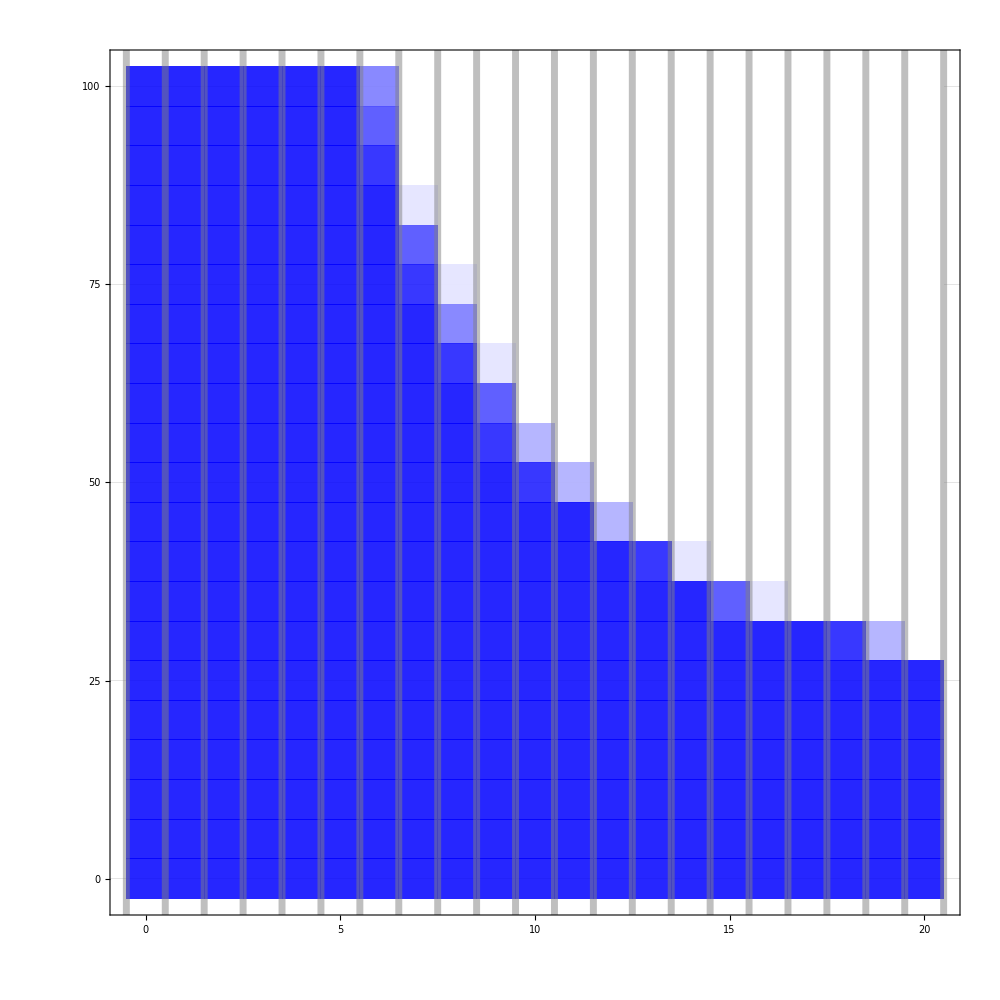

./images/WRYM.png

```mathematica
cf1=(Blend[{Directive[{hexToRGB["#ffffff"],Opacity[1]}],Directive[{RGBColor[0, 0, 1],Opacity[.85]}]},#1]&);
experiment="WRYM";
day=timeRange[[2]];
flattenedData={#[[1]],#[[2]],Round[#[[3]]],#[[4]]}&/@ToExpression[Import[experiment<>".csv"]];
x=If[(StringTake[experiment,{2}]=="X"),0,1];
filtered=If[
(StringTake[experiment,{1}]=="T"),
Cases[flattenedData,{a_,b_,day,c_}->{a,b,x-(x-c)/popsRatio}],
Cases[flattenedData,{a_,b_,day,c_}->{a,b,x-(x-(1-c))/popsRatio}]
];
{firstCol,firstRow}=ConstantArray[x,2];
contour=ListContourPlot[
Flatten[{
filtered,
Transpose[{
ConstantArray[firstCol,flattenedData[[All,2]]//DeleteDuplicates//Length],
flattenedData[[All,2]]//DeleteDuplicates,
ConstantArray[firstRow,flattenedData[[All,2]]//DeleteDuplicates//Length]
}]},1]
,ColorFunction->cf1
,ColorFunctionScaling->False
,GridLines->{Range[-.5,20.5,1],Range[-1.025,1.05,.05]}
,GridLinesStyle->Directive[Gray,Thickness[.005],Opacity[.5]]
,ImageSize->1000
,InterpolationOrder->0
,FrameTicks->{{{#,ToString[#*100//Round]}&/@Range[0,1,.25],None},{Range[0,25,5],None}}
,FrameTicksStyle->Directive[65]
,PlotRange->{{-.5,20.5},{-.025,1.025},{filtered[[All,3]]//Min,filtered[[All,3]]//Max}}
,PlotRangePadding->0
]
Export["./images/"<>experiment<>".png",contour,ImageResolution->500]
```

Response Surface: Fixation/Remediation for Two Nodes

```mathematica
cf1=(Blend[{Directive[{hexToRGB["#ffffff"],Opacity[1]}],Directive[{RGBColor[0, 0, 1],Opacity[.85]}]},#1]&);
Table[
day=timeRange[[2]];
flattenedData={#[[1]],#[[2]],Round[#[[3]]],#[[4]]}&/@ToExpression[Import[experiment<>".csv"]];
x=If[(StringTake[experiment,{2}]=="X"),0,1];
filtered=If[
(StringTake[experiment,{1}]=="T"),
Cases[flattenedData,{a_,b_,day,c_}->{a,b,x-(x-c)/popsRatio}],
Cases[flattenedData,{a_,b_,day,c_}->{a,b,x-(x-(1-c))/popsRatio}]
];
{firstCol,firstRow}=ConstantArray[x,2];
contour=ListContourPlot[
Flatten[{
{#[[1]],#[[2]],If[#[[3]]>1,1,If[#[[3]]<0,0,#[[3]]]]}&/@filtered,
Transpose[{
ConstantArray[firstCol,flattenedData[[All,2]]//DeleteDuplicates//Length],
flattenedData[[All,2]]//DeleteDuplicates,
ConstantArray[firstRow,flattenedData[[All,2]]//DeleteDuplicates//Length]
}]},1]
,ColorFunction->cf1
,ColorFunctionScaling->False
,GridLines->{Range[-.5,20.5,1],Range[-1.025,1.05,.05]}
,GridLinesStyle->Directive[Gray,Thickness[.005],Opacity[.5]]
,ImageSize->1000
,InterpolationOrder->0
,FrameTicks->{{{#,ToString[#*100//Round]}&/@Range[0,1,.25],None},{Range[0,25,5],None}}
,FrameTicksStyle->Directive[65]
,PlotRange->{{-.5,20.5},{-.025,1.025},{0,1}}
,PlotRangePadding->0
];
Export["./images/"<>experiment<>".png",contour,ImageResolution->500]
,{experiment,experimentsList}]
```

{./images/TXYM.png,./images/TRYM.png,./images/UXYM.png,./images/URYM.png,./images/WXYM.png,./images/WRYM.png}

Response Surface (Batch Migration)

```mathematica
day=1093;
experimentString="UB";
multiplier=1000;
flattenedData={#[[1]],#[[2]]*multiplier,Round[#[[3]]],#[[4]]}&/@ToExpression[Import["./"<>experimentString<>".csv"]];
filtered=If[
(StringTake[experimentString,{1}]=="T"),
Cases[flattenedData,{a_,b_,day,c_}->{a,b,c}],
Cases[flattenedData,{a_,b_,day,c_}->{a,b,1-c}]
];
contour=ListDensityPlot[
Flatten[{
filtered,Transpose[{ConstantArray[0,flattenedData[[All,2]]//DeleteDuplicates//Length],flattenedData[[All,2]]//DeleteDuplicates,ConstantArray[0,flattenedData[[All,2]]//DeleteDuplicates//Length]}],Transpose[{flattenedData[[All,1]]//DeleteDuplicates,ConstantArray[0,flattenedData[[All,1]]//DeleteDuplicates//Length],ConstantArray[0,flattenedData[[All,1]]//DeleteDuplicates//Length]}]},1]
,ColorFunction->(Blend[{{1,Directive[RGBColor[1, 1, 1],Opacity[1]]},{0,Directive[RGBColor[1, 0, 0.5],Opacity[1]]}},#]&)
,ColorFunctionScaling->False
,GridLines->{Range[-.5,41,1],Range[.5,25.5,1]}
,GridLinesStyle->Directive[Gray,Thickness[.005],Opacity[.5]]
,ImageSize->1000
,InterpolationOrder->0
(*,FrameLabel->(Style[#,75]&/@{"Releases Number","Coverage"})*)
,FrameTicks->{{{#,ToString[#]}&/@Range[0,25,5],None},{Range[0,40,10],None}}
,FrameTicksStyle->Directive[Bold,65]
,PlotLegends->None
,PlotRange->{{-.5,20.5},{-.5,25.5}}
,PlotRangePadding->0
]
Export["./imagesFinal/BM_"<>experimentString<>".pdf",contour,ImageSize->1000]
```

Response Surface (Sensitivity)

## Single Experiment

```mathematica
day=999;
experimentString="UXSA_200";
flattenedData={#[[1]],#[[2]],Round[#[[3]]],#[[4]]}&/@ToExpression[Import["./"<>experimentString<>".csv"]];
filtered=Cases[flattenedData,{a_,b_,day,c_}->{a,b,1-c}];
{firstCol,firstRow}=ConstantArray[0,2];
contour=ListDensityPlot[
Flatten[{
filtered,
Transpose[{ConstantArray[firstCol,flattenedData[[All,2]]//DeleteDuplicates//Length],
flattenedData[[All,2]]//DeleteDuplicates,ConstantArray[firstRow,flattenedData[[All,2]]//DeleteDuplicates//Length]}]},1]
,ColorFunction->(Blend[{{0,Directive[RGBColor[1, 1, 1],Opacity[1]]},{1,Directive[RGBColor[0, 0, 0.5],Opacity[1]]}},#]&)
,ColorFunctionScaling->False
,GridLines->{Range[-.5,20.5,1],Range[-1.025,1.05,.05]}
,GridLinesStyle->Directive[Gray,Thickness[.005],Opacity[.5]]
,ImageSize->1000
,InterpolationOrder->0
(*,FrameLabel->(Style[#,75]&/@{"Releases Number","Coverage"})*)
,FrameTicks->{{{#,ToString[#*100//Round]}&/@Range[0,1,.25],None},{Range[0,25,5],None}}
,FrameTicksStyle->Directive[65]
,PlotRange->{{-.5,20.5},{-.025,1.025}}
,PlotRangePadding->0
]
Export["./images/"<>experimentString<>".pdf",contour,ImageSize->1000]
```

## Batch Experiment

```mathematica
expIDS={"T","U"};
expIDN=Flatten[{("XSA_"<>#),("RSA_"<>#)}&/@{"001","002","010","020","100","200"}];
expStrings=Table[(i<>#)&/@expIDN,{i,expIDS}]
```

```mathematica
Table[
Table[
experimentString=expStrings[[i,j]];
(**)
flattenedData={#[[1]],#[[2]],Round[#[[3]]],#[[4]]}&/@ToExpression[Import["./"<>experimentString<>".csv"]];
filtered=Cases[flattenedData,{a_,b_,day,c_}->{a,b,c}];
filtered=If[i==1,filtered,{#[[1]],#[[2]],1-#[[3]]}&/@filtered];
{firstCol,firstRow}=If[(i==1)&&(StringTake[experimentString,{2}]=="R"),ConstantArray[0,2],ConstantArray[1,2]];
{firstCol,firstRow}=If[(i==2)&&(StringTake[experimentString,{2}]=="X"),ConstantArray[0,2],ConstantArray[1,2]];
(**)
contour=ListDensityPlot[
Flatten[{
filtered,
Transpose[{ConstantArray[firstCol,flattenedData[[All,2]]//DeleteDuplicates//Length],
flattenedData[[All,2]]//DeleteDuplicates,ConstantArray[firstRow,flattenedData[[All,2]]//DeleteDuplicates//Length]}]},1]
,ColorFunction->(Blend[{{0,Directive[RGBColor[1, 1, 1],Opacity[1]]},{1,Directive[RGBColor[0, 0, 0.5],Opacity[1]]}},#]&)
,ColorFunctionScaling->False
,GridLines->{Range[-.5,20.5,1],Range[-1.025,1.05,.05]}
,GridLinesStyle->Directive[Gray,Thickness[.005],Opacity[.5]]
,ImageSize->1000
,InterpolationOrder->0
(*,FrameLabel->(Style[#,75]&/@{"Releases Number","Coverage"})*)
,FrameTicks->{{{#,ToString[#*100//Round]}&/@Range[0,1,.25],None},{Range[0,25,5],None}}
,FrameTicksStyle->Directive[65]
,PlotRange->{{-.5,20.5},{-.025,1.025}}
,PlotRangePadding->0
];
Export["./imagesFinal/SA_N_"<>experimentString<>".pdf",contour,ImageSize->1000]
,{j,1,Length[expStrings[[i]]]}]
,{i,1,2}]
```

Response Surface (Sensitivity Difference)

## Single Experiment

```mathematica
experimentString="UXSA_0002Diff";
{firstCol,firstRow}=ConstantArray[0,2];
flattenedData=Chop[Import["./"<>experimentString<>".csv"],10^-2];
{flattenedData[[All,3]]//Max,flattenedData//Min}
flattenedData[[All,3]]//Sort;
dominant=If[Total[flattenedData[[All,3]]]<0,-1,1];
flattenedData={#[[1]],#[[2]]*10,If[#[[3]]<0,#[[3]],dominant*(#[[3]])]}&/@flattenedData;
```

{0.17087,-0.05866}

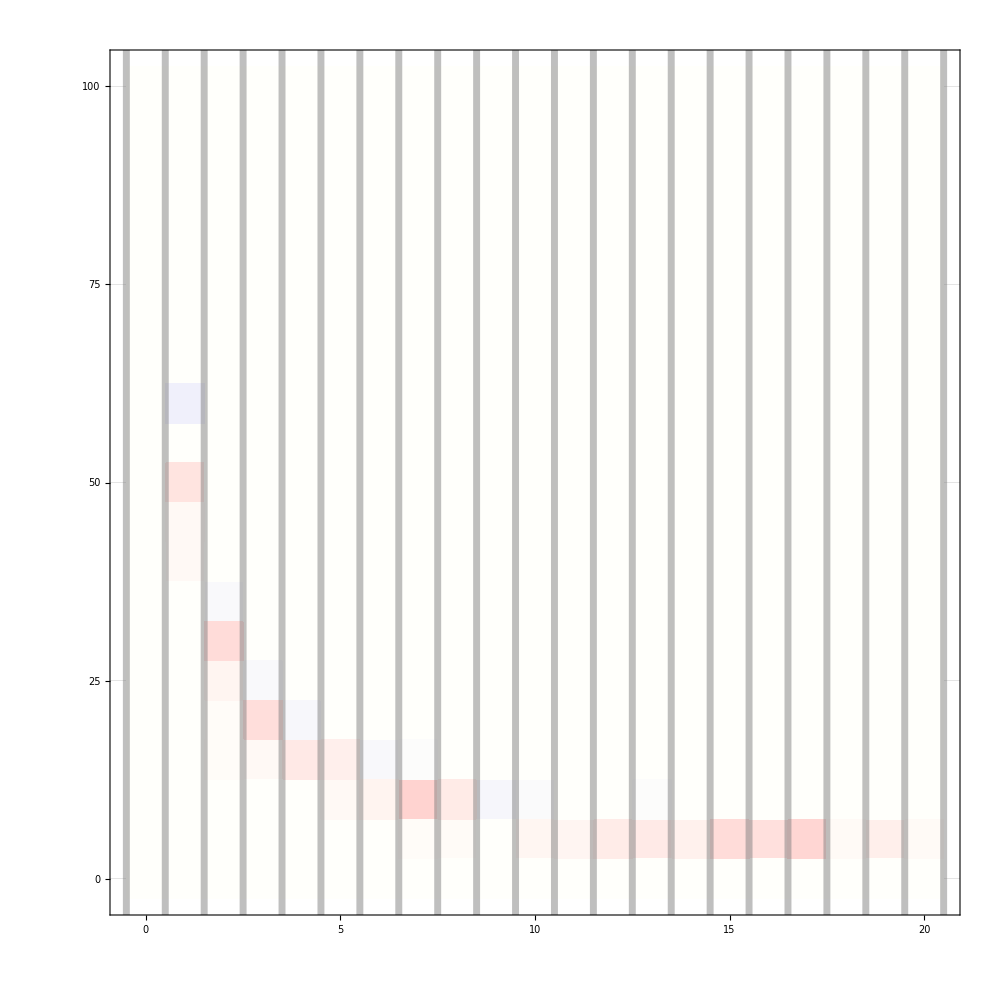

./images/UXSA_0002Diff.pdf

```mathematica
contour=ListDensityPlot[Flatten[{flattenedData,Transpose[{ConstantArray[firstCol,flattenedData[[All,2]]//DeleteDuplicates//Length],flattenedData[[All,2]]//DeleteDuplicates,ConstantArray[0,flattenedData[[All,2]]//DeleteDuplicates//Length]}]},1]
,ColorFunction->(Blend[{{-1,Directive[RGBColor[0.0006103608758678569, 0., 1],Opacity[1]]},{0,Directive[RGBColor[1, 1, 0.9850156404974442],Opacity[1]]},{1,Directive[RGBColor[1, 0, 0],Opacity[1]]}},#]&)
,ColorFunctionScaling->False
,ClippingStyle->Black
,GridLines->{Range[-.5,20.5,1],Range[-102.5,100.5,5]}
,GridLinesStyle->Directive[Gray,Thickness[.005],Opacity[.5]]
,ImageSize->1000
,InterpolationOrder->0
(*,FrameLabel->(Style[#,75]&/@{"Releases Number","Coverage"})*)
,FrameTicks->{{{#,ToString[#*1//Round]}&/@Range[0,100,25],None},{Range[0,25,5],None}}
,FrameTicksStyle->Directive[65]
,PlotRange->{{-.5,20.5},{-2.5,102.5},{-1,1}}
,PlotRangePadding->0
]
Export["./images/"<>experimentString<>".pdf",contour,ImageSize->1000]
```

## Batch Experiment

```mathematica
expIDS={"T","U"};
expIDN=Flatten[{("XSA_"<>#<>"Diff"),("RSA_"<>#<>"Diff")}&/@{"001","002","010","020","100","200"}];
expStrings=Table[(i<>#)&/@expIDN,{i,expIDS}]
```

```mathematica
Table[
Table[
experimentString=expStrings[[i,j]];
{firstCol,firstRow}=ConstantArray[0,2];
flattenedData=Chop[Import["./"<>experimentString<>".csv"],10^-2];
dominant=If[Total[flattenedData[[All,3]]]<0,-1,1];
flattenedData={#[[1]],#[[2]],If[#[[3]]<0,#[[3]],1*(#[[3]])]}&/@flattenedData;
flattenedData=If[i==1,flattenedData,{#[[1]],#[[2]],-1*#[[3]]}&/@flattenedData];
(**)
contour=ListDensityPlot[Flatten[{flattenedData,Transpose[{ConstantArray[firstCol,flattenedData[[All,2]]//DeleteDuplicates//Length],flattenedData[[All,2]]//DeleteDuplicates,ConstantArray[0,flattenedData[[All,2]]//DeleteDuplicates//Length]}]},1]
,ColorFunction->(Blend[{{-1,Directive[RGBColor[0.0006103608758678569, 0., 1],Opacity[1]]},{0,Directive[RGBColor[1, 1, 0.9850156404974442],Opacity[1]]},{1,Directive[RGBColor[1, 0, 0],Opacity[1]]}},#]&)
,ColorFunctionScaling->False
,ClippingStyle->Black
,GridLines->{Range[-.5,20.5,1],Range[-1.025,1.05,.05]}
,GridLinesStyle->Directive[Gray,Thickness[.005],Opacity[.5]]
,ImageSize->1000
,InterpolationOrder->0
(*,FrameLabel->(Style[#,75]&/@{"Releases Number","Coverage"})*)
,FrameTicks->{{{#,ToString[#*100//Round]}&/@Range[0,1,.25],None},{Range[0,25,5],None}}
,FrameTicksStyle->Directive[65]
,PlotRange->{{-.5,20.5},{-.025,1.025},{-1,1}}
,PlotRangePadding->0
];
Export["./imagesFinal/SA_D_"<>experimentString<>".pdf",contour,ImageSize->1000]
,{j,1,Length[expStrings[[i]]]}]
,{i,1,2}]
```

Response Surface (Batch Migration Sensitivity)

```mathematica
day=1093;
experimentString="UBSA_200Diff";
multiplier=1;
flattenedData=Chop[Import["./"<>experimentString<>".csv"],10^-2];
(*{flattenedData[[All,3]]//Max,flattenedData//Min}
flattenedData[[All,3]]//Sort;
dominant=If[Total[flattenedData[[All,3]]]<0,-1,1];
flattenedData={#[[1]],#[[2]]*multiplier,2*If[#[[3]]<0,#[[3]],dominant*(#[[3]])]}&/@flattenedData;*)
ListDensityPlot[flattenedData,InterpolationOrder->0];
flattenedData[[All,3]]//Sort;
```

```mathematica
contour=ListDensityPlot[Flatten[{flattenedData,Transpose[{flattenedData[[All,1]]//DeleteDuplicates,ConstantArray[0,flattenedData[[All,1]]//DeleteDuplicates//Length],ConstantArray[0,flattenedData[[All,1]]//DeleteDuplicates//Length]}]},1]
,ColorFunction->(Blend[{{-1,Directive[RGBColor[0.0006103608758678569, 0., 1],Opacity[1]]},{0,Directive[RGBColor[1, 1, 0.9850156404974442],Opacity[1]]},{1,Directive[RGBColor[1, 0, 0],Opacity[1]]}},#]&)
,ColorFunctionScaling->False
,GridLines->{Range[-.5,41,1],Range[-.005,.25,.01]}
,GridLinesStyle->Directive[Gray,Thickness[.005],Opacity[.5]]
,ImageSize->1000
,InterpolationOrder->0
(*,FrameLabel->(Style[#,75]&/@{"Releases Number","Coverage"})*)
,FrameTicks->{{{#,ToString[#*100//Round]}&/@Range[0,.25,.05],None},{Range[0,40,10],None}}
,FrameTicksStyle->Directive[Bold,65]
,PlotLegends->None
,PlotRange->{{-.5,20.5},{-.005,.255},{-1,1}}
,PlotRangePadding->0
]
Export["./images/"<>experimentString<>".pdf",contour,ImageSize->1000]
```

Timing

```mathematica
experimentString=experimentString="50UX_1x_2018_09_04";
flattenedData=Import["./"<>experimentString<>".csv"];
```

```mathematica
Table[
coverage=i;
releasesNumber=flattenedData[[All,1]]//DeleteDuplicates;
probed=Cases[flattenedData,{#,coverage,_,c_}->1-c]&/@releasesNumber;
plot=ListLinePlot[probed
,AspectRatio->1
,Filling->Prepend[(#->{#+1})&/@Range[1,Length[probed]-1],1->1]
,FillingStyle->Opacity[0]
,Frame->True
,FrameStyle->Directive[Thickness[.0075],Gray,50]
,FrameTicks->None(*{{{#,StringPadRight[ToString[#],4,"0"]}&/@Range[0,1,.5],None},{Flatten[{Range[0,1000,200]}],None}}*)
,FrameTicksStyle->30
,GridLines->{Range[0,1000,200],Range[0,1,.25]}
,GridLinesStyle->Directive[Gray,Thick,Opacity[.2]]
,ImageSize->1000
,InterpolationOrder->0
,PlotRange->{{9*20,1000},{0,1}}
,PlotStyle->({Thickness[.005],Blend[{{0,Directive[RGBColor[1, 0.5, 1],Opacity[1]]},{1,Directive[RGBColor[0, 0, 1],Opacity[1]]}},#]}&/@Range[0,1,.05])
,Prolog->Flatten[{Opacity[.2],Dashed,Thickness[.001],Line[{{#,0},{#,1}}]&/@(Range[0,7*20-1,1*7]+20)}]
];
Export["./"<>experimentString<>"_"<>StringPadLeft[ToString[coverage*100//Round],4,"0"]<>".png",plot,ImageSize->1000]
,{i,flattenedData[[All,2]]//DeleteDuplicates}]
```

```mathematica
Line[{ConstantArray[0,probed[[2]]//Length],Range[1,probed[[2]]//Length],probed[[2]]}//Transpose]
```

```mathematica
Range[First[releasesNumber],Last[releasesNumber],4]
releasesNumber
```

```mathematica
two=Blend[{{0,Directive[RGBColor[1, 0.5, 1],Opacity[1]]},{1,Directive[RGBColor[0, 0, 1],Opacity[1]]}},#]&/@Range[0,1,1]
SwatchLegend[two,{"1 release","20 releases"}]
```

```mathematica
BarLegend[{Blend[{{0,Directive[RGBColor[1, 0.5, 1],Opacity[1]]},{1,Directive[RGBColor[0, 0, 1],Opacity[1]]}},#]&,{0,1}},20]
Export["swatch.pdf",%,ImageSize->1000]
```

```mathematica
(#->{#+1})&/@Range[2,10]
```

Legends

```mathematica
BarLegend[{(Blend[{{0,Directive[RGBColor[1, 1, 1],Opacity[1]]},{1,Directive[RGBColor[1, 0, 0.5],Opacity[1]]}},#]&),{0,1}}]
Export["./images/colorScaleBatch.pdf",%,ImageSize->500]
BarLegend[{(Blend[{Directive[{hexToRGB["#ffffff"],Opacity[1]}],Directive[{RGBColor[0, 0, 1],Opacity[.85]}]},#1]&),{0,1}}]
Export["./images/colorScale.pdf",%,ImageSize->500]
BarLegend[{(Blend[{{0,Directive[RGBColor[1, 1, 1],Opacity[1]]},{1,Directive[RGBColor[0, 0, 0.5],Opacity[1]]}},#]&),{0,1}}]
Export["./images/colorScaleSensitivity.pdf",%,ImageSize->500]
```

./images/colorScaleBatch.pdf

./images/colorScale.pdf

./images/colorScaleSensitivity.pdf

```mathematica
SwatchLegend[
{ColorData[{"DeepSeaColors",{0,1}}][0],ColorData[{"DeepSeaColors",{0,1}}][1]},
{"0% Drive","100% Drive"}
,LegendMarkerSize->50
,LabelStyle->50
]
Export["swatchFixation.pdf",%]
```